# Implicit Function Graphing and Differentiation

## Plotting implicitly defined functions

```mathematica
Clear[x,y]
```

### Plotting the devil’s curve

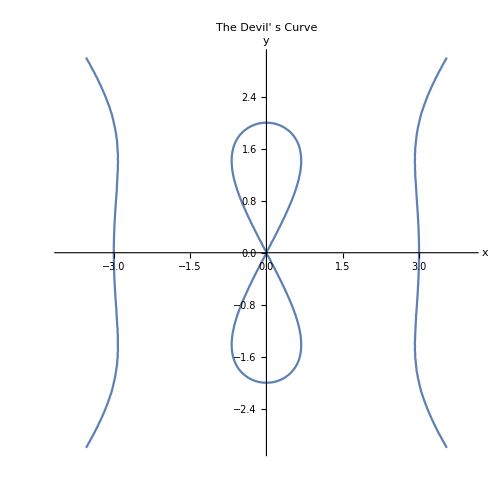

```mathematica
ContourPlot[y^4-4  y^2==x^4-9  x^2, {x, -4,4},{y,-3,3},Axes->True,AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0],Bold},PlotLabel->HoldForm[The Devil's Curve],Frame-> False]
```

### Implicit differentiation

By default Mathematica treats variables as independent. So for example D[y,x] produces 0. Entering y[x] in place of y however tells Mathematica to treat y as a function of x. This enables implicit differentiation. 

We will use the devil’s curve as our example.

```mathematica
equa = (y[x]^4-4 y[x]^2== x^4-9 x^2);
```

We will use the Solve[] and D[] functions to complete the implicit differentiation.

```mathematica
m = Solve[D[equa,x],y'[x]]
```

{{y'[x]→(-9 x+2 x^3)/(2 y[x] (-2+y[x]^2))}}

### The Graph of a Implicit Function

Let’s now apply this result to plot the devil’s curve together with its tangent lines at the point x = 1/2.

```mathematica
yvalues = y/.Solve[y^4-4 y^2==x^4-9 x^2/.x-> 0.5];
tanvalues = Table[(m/.{x->0.5,y[x]->yvalues[[i]]})(x-0.5)+yvalues[[i]],{i,4}];
```

```mathematica
Clear[point1,point2, p1,p2]
```

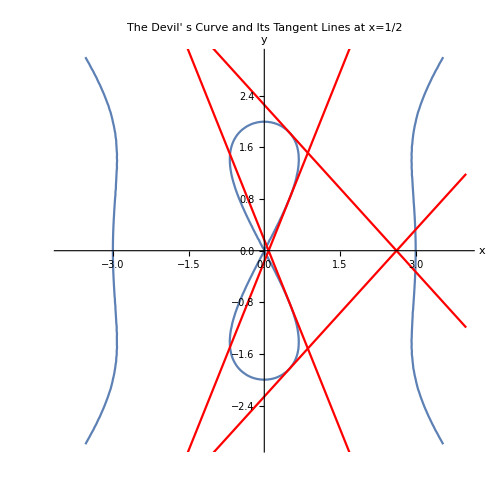

```mathematica
point1 = ContourPlot[y^4-4 y^2==x^4-9 x^2,{x,-4,4},{y,-3,3},Axes->True,AxesLabel->{"x","y"},Frame->False,DisplayFunction->Identity];
point2 = Plot[tanvalues,{x,-4,4},PlotStyle->Red,DisplayFunction->Identity];
Show[point1,point2,PlotLabel->HoldForm[The Devil' s Curve and Its Tangent Lines at x=1/2],LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0],Bold}]
```